## Setup

```mathematica
afinesdir="/home/simonfreedman/Code/cytomod/";
trajdir="/project/weare-dinner/simonfreedman/cytomod/out/design/trajs/";
figdir="/project/weare-dinner/simonfreedman/cytomod/out/design/figs/";
```

```mathematica
Import[afinesdir<>"/analysis/cytomod_functions.m"];
```

```mathematica
nf1[x_]:=NumberForm[x,{2,1}];
nf2[x_]:=NumberForm[x,{2,2}];

importsum[f_]:=With[{dat=importCheck[f]},{Total[dat],Length[dat]}];

intv[vac_,ti_:1,tf_:-1]:=Total[0.5(vac[[(ti+1);;tf,2]]+vac[[ti;;(tf-1),2]])(vac[[(ti+1);;tf,1]]-vac[[ti;;(tf-1),1]])];
gt[x_,y_]:=If[x>y,1,0];


ClearAll[intmeangrb,intmeangr,meshavg];
intmeangr[dir_,ti_:1,tf_:50,maxr_:100,file_:grf]:=With[{grdat=importCheck[dir<>file]},
If[Dimensions[grdat][[2]]==1,intv[Mean[grdat[[ti;;tf,1,1;;maxr]]]],intv[Mean[grdat[[ti;;tf,1;;maxr]]]]]
];
intmeangrb[dir_,ti_:1,tf_:50,maxr_:100,grf_:grf, grbf_:grbf]:=intv@With[
{grdat=importCheck[dir<>grf],grbdat=importCheck[dir<>grbf]},
If[Dimensions[grdat][[2]]==1,
{grbdat[[ti,1,2;;maxr,1]],Mean[grbdat[[ti;;tf,1,2;;maxr,2]]]/Mean[grdat[[ti;;tf,1,2;;maxr,2]]]}ᵀ,
{grbdat[[1,2;;maxr,1]],Mean[grbdat[[ti;;tf,2;;maxr,2]]]/Mean[grdat[[ti;;tf,2;;maxr,2]]]}ᵀ,
]
];
meshavg[dir_,meshsizef_:meshsizef]:=Mean[Flatten[importCheck[dir<>meshsizef]]];
```

```mathematica
seedMdensXldens=
Table[StringJoin[ToString/@{trajdir,"dens_dens/seed",sd,"e7_mdens",nf2@md,"_xldens",nf1@xd}],
{sd,1,5},
{md,{0,0.01,0.02,0.05,0.1,0.2,0.3}},
{xd,{0,0.1,0.2,0.5,0.8,1,1.2,1.5}}
];
```

```mathematica
seedMkoffXlkoff=
Table[StringJoin[ToString/@{trajdir,"koff_koff_len/seed",sd,"e7_len10_mkoff",nf2@mk,"_xlkoff",nf2@xlk}],
{sd,1,5},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}},
{xlk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenMkoff=
Table[StringJoin[ToString/@{trajdir,"mkoff_len/seed",sd,"e7_len",len,"_mkoff",nf2@mk}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenXlkoff=
Table[StringJoin[ToString/@{trajdir,"xlkoff_len/seed",sd,"e7_len",len,"_xlkoff",nf2@mk}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenMkoffXlkoff20=
Table[StringJoin[ToString/@{trajdir,"koff_koff_len/seed",sd,"e7_len",len,"_mkoff",nf2@mk,"_xlkoff0.05"}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];
```

```mathematica
seedLenXlkoffMkoff5=
Table[StringJoin[ToString/@{trajdir,"koff_koff_len/seed",sd,"e7_len",len,"_mkoff0.20_xlkoff",nf2@mk}],
{sd,1,5},
{len,{1,2,5,8,10,15}},
{mk,{0.01,0.02,0.05,0.1,0.2,0.5,1}}
];


forestgreen=RGBColor[34/255,139/255,34/255];
```

```mathematica
(*bpscsd1=Flatten@seedMdensXldens[[1,{1,-1},{1,-1}]];
bpscsds=Flatten/@seedMdensXldens[[All,{1,-1},{1,-1}]];*)
```

## Order parameter calculations

These calculations are potentially slow, so its best to do them on the different trajectories in parallel, if you have access to mathematica command line, using listed scripts, as described in README.md

### g (r)

### g(r_barb)

### mesh size

### msd

### angle distribution

## Phase Portraits (Figs. 1, S1, S2, S5, S6, S7,S9C)

### 1

```mathematica
phasespace=Flatten@seedMdensXldens[[1,{1,4,7},{1,5,8}]];
```

```mathematica
lks=ParallelTable[pts2[dr,"links"][[-1]],{dr,phasespace}];
ams=ParallelTable[pts2[dr,"amotors"][[-1]],{dr,phasespace}];
pms=ParallelTable[pts2[dr,"pmotors"][[-1]],{dr,phasespace}];
```

```mathematica
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
ddphases=GraphicsGrid[Reverse@(Partition[frs[[All,1]],3]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
Export[figdir<>"/f1.eps",ddphases];
```

### S1

```mathematica
frs=Table[draw[{},{lks[[i]]},
If[Dimensions[ams[[i]]][[2]]==8,{ams[[i,1;;-1;;1]]},{}],
If[Dimensions[pms[[i]]][[2]]==8,{pms[[i,1;;-1;;1]]},{}],
"",False,{50,50},True,11],{i,Length[ams]}];
ddphases=GraphicsGrid[Reverse@(Partition[frs[[All,1]],3]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
Export[figdir<>"/fs1.eps",ddphases];
```

### S2

```mathematica
ac=pts2[phasespace[[3]],"actins"][[-1,All,1;;2]];
```

```mathematica
np=500;
nm=11;
nsb=10;
fov={50,50};
acallb=Table[mysubdivide[ac[[j*nm+i]],ac[[j nm+i+1]],nsb,fov],{j,0,np-1},{i,1,nm-1}];
acplt=ListPlot[Flatten[acallb,2],Joined->False,PlotStyle->Red,PlotMarkers->{●,5},PlotRange->25{{-1,1},{-1,1}},FrameTicks->None,AspectRatio->1,Axes->None];
```

```mathematica
thresh=1;
vxsz=0.25;
nbxs=fov[[1]]/vxsz;
bncnts=BinCounts[Flatten[acallb,2],{-0.5fov[[1]],0.5fov[[2]],vxsz},{-0.5fov[[1]],0.5fov[[2]],vxsz}];
bc=Map[If[#>=thresh,1,0]&,bncnts,{2}];
```

```mathematica
sp0s=Table[SequencePosition[bc[[All,t]],{Repeated[0]},Overlaps->False],{t,Length[bc]}];
d=ConstantArray[0,{200,200}];
Do[d[[i,z[[1]];;z[[2]]]]=z[[2]]-z[[1]],{i,Length[sp0s]},{z,sp0s[[i]]}];

sp0sCol=Table[SequencePosition[bc[[t]],{Repeated[0]},Overlaps->False],{t,Length[bc]}];
dCol=ConstantArray[0,{200,200}];
Do[dCol[[i,z[[1]];;z[[2]]]]=z[[2]]-z[[1]],{i,Length[sp0sCol]},{z,sp0sCol[[i]]}];

dat=0.25/2Reverse@(dColᵀ+d);
```

```mathematica
cf=ColorData[{"SunsetColors","Reversed"}];
plt=Show[ArrayPlot[Log10@(dat+0.125),ColorFunction->cf,ColorFunctionScaling->True],
ArrayPlot[Reverse@Transpose@bc,ColorFunction->(If[#>0,Black,Transparent]&)]
]
```

```mathematica
leg=logbarleg[Min[dat+0.125],Max[dat+0.125],4,cf,NumberForm[#-0.125,{2,1}]&,{LegendMarkerSize->{30,300},LabelStyle->Directive[Black,FontSize->22],LegendLabel->Placed[Rotate["mesh size (μm)",3Pi/2],Right]}]
```

```mathematica
Export[figdir<>"/S4.pdf",plt];
Export[figdir<>"/S4leg.pdf",leg];
```

### S5

```mathematica
phasespace=Flatten@seedMkoffXlkoff[[2,{1,3,5,7},{1,3,5,7}]];
```

```mathematica
lks=ParallelTable[pts2[dr,"links"][[400]],{dr,phasespace}];
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
```

```mathematica
phases=Show[GraphicsGrid[(Transpose@Reverse@Partition[frs[[All,1]],4]),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]],Frame->True,FrameLabel->{"1/k_m^off (s)","1/k_xl^off (s)"},FrameTicks->{
{{{-1250,1},{-900,5},{-550,20},{-200,100}},None},
{{{200,1},{550,5},{900,20},{1250,100}},None}},FrameStyle->Directive[FontSize->16,Black]];;
```

```mathematica
phases
```

```mathematica
Export[figdir<>"/fs5.eps",phases];
```

### S6

```mathematica
phasespace=Flatten@seedLenMkoff[[2,{1,4,5,6},{1,4,5,7}]];
```

```mathematica
lks=ParallelTable[pts2[dr,"links"][[400]],{dr,phasespace}];
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
```

```mathematica
phases=Show[GraphicsGrid[(Partition[Reverse@frs[[All,1]],4]),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]],Frame->True,FrameLabel->{"1/k_m^off (s)","filament length (μm)"},FrameTicks->{
{{{-1250,1},{-900,8},{-550,10},{-200,15}},None},
{{{200,1},{550,5},{900,10},{1250,100}},None}},FrameStyle->Directive[FontSize->16,Black]];
```

```mathematica
phases
```

```mathematica
Export[figdir<>"/fs6.eps",phases];
```

### S7

```mathematica
phasespace=Flatten@seedLenXlkoff[[2,{1,3,4,6},{1,3,4,7}]];
```

```mathematica
lks=ParallelTable[pts2[dr,"links"][[400]],{dr,phasespace}];
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
```

```mathematica
phases=Show[GraphicsGrid[(Partition[Reverse@frs[[All,1]],4]),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]],Frame->True,FrameLabel->{"1/k_xl^off (s)","filament length (μm)"},FrameTicks->{
{{{-1250,1},{-900,5},{-550,8},{-200,15}},None},
{{{200,1},{550,10},{900,20},{1250,100}},None}},FrameStyle->Directive[FontSize->16,Black]];
```

```mathematica
phases
```

```mathematica
Export[figdir<>"/fs7.eps",phases];
```

### S9C

```mathematica
phasespace=Flatten@seedMdensXldens[[1,{1,7},{1,8}]];
```

```mathematica
lks=ParallelTable[pts2[dr,"links"][[-1]],{dr,phasespace}];
```

```mathematica
frs=Table[draw[{},{lk},{},{},"",False,{50,50},True,11],{lk,lks}];
ddphases=GraphicsGrid[Reverse@(Partition[frs[[All,1]],2]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
Export[figdir<>"/S10C_lks.eps",ddphases];
```

```mathematica
ti=1;tf=30000;
amots=pts2[#<>"/restart_more_motors_long_kend10/seed1e6","amotors"]&/@phasespace;
amotcms=amots[[All,ti;;tf,1,1;;2]]+0.5amots[[All,ti;;tf,1,3;;4]];
```

```mathematica
cf=ColorData[{"BlueGreenYellow",{ti,tf}}];
myline[xy_,col_,thickness_,max_:10]:=If[Norm[xy[[1]]-xy[[2]]]≤max,{col,Thickness[thickness],Line[xy]},Nothing];
ls=Table[myline[amotcms[[i,t;;(t+1)]],cf[t],0.005],{i,Length[amotcms]},{t,ti,tf-1}];
```

```mathematica
frms=Table[Graphics[ls[[i]],PlotRange->{{-25,25},{-25,25}}],{i,Length[ls]}];
trajs=GraphicsGrid[Reverse@(Partition[frms,2]ᵀ),Spacings->{0,0},Frame->All,FrameStyle->Directive[Black,Thickness[0.005]]];
```

```mathematica
Export[figdir<>"/S10C_mots.eps",trajs];
```

## Structural Consequences (Figs 2, 5, S8, S9A-B)

### plotting settings

```mathematica
bpscdirs=Transpose@(Flatten/@seedMdensXldens[[{1,3,5},{1,-1},{1,-1}]]);

th=0.012;
th2=0.008;
pss={Directive[Black,Thickness[th2]],Directive[Lighter@Blue,Thickness[th]],Directive[forestgreen,Thickness[th]],Directive[Red,Thickness[th]]};
leg=PointLegend[{"homogenous","bundled","polarity sorted","contracted"},Spacings->0,LabelStyle->FontSize->22,LegendMarkerSize->20];
```

### 2 A

Preprocessing : requires gr script to be run on bpscdirs (last 50 s only)

```mathematica
grf="/analysis/gr_dr0.05_maxr25t351-400.dat";
grdats=Map[importCheck[#<>grf][[All,1]]&,bpscdirs,{2}];
mugrs=Table[{gr[[1,All,1]]+0.025,Mean[gr[[All,All,2]]]}ᵀ,{gr,Flatten[#,1]&/@grdats}];
```

```mathematica
p1=ListPlot[mugrs,
PlotMarkers->None,
PlotStyle->pss,
PlotRange->{{0,11.8},{0,36.5}},
FrameLabel->{"r (μm)","g(r)"},
Joined->True];
```

```mathematica
Export[figdir<>"/2A.svg",p1];
```

```mathematica
p2=ListPlot[mugrs,
PlotMarkers->None,
PlotStyle->pss,
PlotRange->{{0,2.5},{0.7,6.9}},
FrameTicks->{{LinTicks[0,8,2,10],Automatic},{LinTicks[0,3,1,10],Automatic}},
Joined->True,
BaseStyle->FontSize->36];
```

```mathematica
Export[figdir<>"/2Ainset.svg",p2];
```

### 2 B

Preprocessing : requires gr_barbed and gr script to be run on bpscdir (last 50 s only)

```mathematica
grbf="/analysis/gr_barbed_dr0.05_maxr25t351-400.dat";
grbdats=Map[importCheck[#<>grbf][[All,1]]&,bpscdirs,{2}];
```

```mathematica
grdatsf=Flatten[#,1]&/@grdats;
grbdatsf=Flatten[#,1]&/@grbdats;
mugrbs=Table[{grbdatsf[[i,1,All,1]]+0.025,Mean[grbdatsf[[i,All,All,2]]]/Mean[grdatsf[[i,All,All,2]]]}ᵀ,{i,Length[grbdatsf]}];
```

```mathematica
p1=ListPlot[mugrbs,
PlotMarkers->None,
PlotStyle->pss,
PlotRange->{{0,2.65},{0,57}},
FrameLabel->{"r (μm)","g(r_barb)/g(r)"},
Axes->{False,True},AxesOrigin->{0.5,0},AxesStyle->Directive[Black,Thickness[0.007],Dashed],
PlotLegends->Placed[leg,{0.65,0.7}]
];
```

```mathematica
p1
```

```mathematica
Export[figdir<>"/2B.svg",p1];
```

### 2 C

Preprocessing : requires mesh size and gr script to be run on bpscdirs (whole trajectory)

```mathematica
meshsizef="/analysis/meshsizes_1D_vx0.25_thresh1_t351-400.dat";
dats=Map[importCheck[#<>meshsizef][[All,1]]&,bpscdirs,{2}];
```

```mathematica
maxr=48;
minr=0;
dr=0.25;
bcs=Table[BinCounts[Flatten[dats[[i]]],{minr,maxr,dr}],{i,Length[dats]}];
probs=bcs/(dr*Total/@bcs);
```

```mathematica
plt=ListPlot[probs,DataRange->{minr,maxr},
PlotRange->{{-1,44},Full},
PlotMarkers->None,
PlotStyle->pss,
FrameLabel->{"mesh size (μm)","probability density"},PlotRange->Full]
```

```mathematica
Export[figdir<>"/2C.svg",plt];
```

```mathematica
meshsizefullf="/analysis/meshsizes_1D_vx0.25_thresh1_t1-400.dat";
msdatsfull=Map[(Mean[Flatten[#]]&)/@importCheck[#<>meshsizefullf]&,bpscdirs,{2}];
```

```mathematica
rmax=5;
dr=0.05;
grfullf="/analysis/gr_dr0.05_maxr25t1-400.dat";
grints=Map[((intv[#,1,Round[rmax/dr]]/rmax&)/@(importCheck[#<>grfullf][[All,1]]))&,bpscdirs,{2}];
```

```mathematica
mspltdat=msdatsfull/grints;
```

```mathematica
plt=ListPlot[Mean/@mspltdat,
PlotMarkers->None,
PlotStyle->pss,
FrameLabel->{"time (s)","⟨mesh size⟩ / ⟨g(r)⟩  "},
PlotRange->{Full,{1,3.6}},
FrameTicks->{{Table[If[MemberQ[{1.,2.,3.},i],{i,ToString@integerize@i,{0.02,0}},{i,"",{0.01,0}}],{i,1,4,0.1}],Automatic},
{Table[If[MemberQ[{0,200,400},i],{i,ToString@i,{0.02,0}},{i,"",{0.01,0}}],{i,0,400,20}],Automatic
}},FrameStyle->Directive[Black,FontSize->28],
FrameTicksStyle->Directive[Black,FontSize->30]];
```

```mathematica
plt
```

```mathematica
Export[figdir<>"/2Cinset.svg",plt];
```

### 2D

Preprocessing : requires velocity field python script to be run, and divergence / bin count script to be run on bpscdirs

```mathematica
thresh=5;
divfname="/analysis/div_dr1_nbins10_thresh10_dt10.dat";
bcfname="/analysis/bin_counts_dr1.dat";
divthresh[dir_,thresh_]:=Module[{},
divf=importCheck[dir<>divfname];
bcf=importCheck[dir<>bcfname];
bcft=MovingAverage[0.5(bcf[[2;;]]+bcf[[;;-2]]),10];
bcfti=Map[gt[#,thresh]&,bcft,{3}];
Map[Mean[Flatten[#]]&,bcfti*divf]
];
```

```mathematica
divthreshs=Map[divthresh[#,thresh]&,bpscdirs,{2}];
```

```mathematica
tf=389;
divthavg=Mean/@divthreshs[[All,All,1;;tf]];
```

```mathematica
plt=ListPlot[MovingAverage[#,1]&/@divthavg*1000,Joined->True,PlotRange->Full,PlotMarkers->None,PlotStyle->pss,FrameLabel->{"time (s)",Style["⟨∇·v_a⟩ (10^-3s^-1)",SingleLetterItalics->False]},FrameTicks->{{Automatic,Automatic},{{#,If[Mod[#,100]==0,#,""]}&/@Range[0,400,10],Automatic}},PlotLegends->None]
```

```mathematica
Export[figdir<>"/2D.svg",plt];
```

### 5 A

Preprocessing : requires angle distribution code to be run on all 1250 (125 groups of 10) motor trajectories from t=5000-30000 s for all bpscdirs

```mathematica
motds=Table["/restart_more_motors_long/seed"<>ToString[s]<>"e6/",{s,1,125}];
angbcfs="/analysis/vmot_anghist2_t5000-30000d"<>ToString[#]<>"dth0.001_zvalNothing.dat"&/@{1,2,5,10,20,50,100,200,500,1000};
angbcs=ParallelTable[importCheck[bpscdirs[[i,j]]<>motd<>bcf],{i,Length[bpscdirs]},{j,Length[bpscdirs[[i]]]},{motd,motds},{bcf,angbcfs}];
```

```mathematica
angbctots=Table[Total[angbcs[[i,All,All,k,All,1]],2],{i,4},{k,10}];
angfreqs=Table[angbctots[[i,j]]/(0.001Total[angbctots[[i,j]]]),{i,1,Length[angbctots]},{j,Length[angbctots[[i]]]}];
ds=5;
angbctotsrb=Table[Total[angbctots[[i,j,k;;(k+ds-1)]]],{i,4},{j,10},{k,1,1000,ds}];
angfreqsrb=Table[angbctotsrb[[i,j]]/(ds*0.001Total[angbctotsrb[[i,j]]]),{i,1,Length[angbctotsrb]},{j,Length[angbctotsrb[[i]]]}];
```

```mathematica
ft={{LinTicks[0,6,1,4],LinTicks[0,6,1,4,ShowTickLabels->False]},Automatic};
pr={{-0.01,1.01},{0,4.2}};
fl={"θ/2π","P(θ)"};
```

```mathematica
ps=Table[ListPlot[angfreqsrb[[All,i]],DataRange->{0,1},PlotRange->pr,PlotStyle->pss,PlotMarkers->None,AspectRatio->0.4,FrameTicks->ft,FrameLabel->fl,BaseStyle->FontSize->28],{i,1,Length[angfreqsrb[[1]]]}];
```

```mathematica
ps[[1]]
```

```mathematica
ps[[6]]
```

```mathematica
Export[figdir<>"/5Atop.svg",ps[[1]]];
Export[figdir<>"/5Amid.svg",ps[[6]]];
Export[figdir<>"/5Abot.svg",ps[[10]]];
```

### S8 C

```mathematica
ps2=Table[ListPlot[angfreqsrb[[i,All]],DataRange->{0,1},PlotRange->pr,PlotStyle->"BlueGreenYellow",PlotMarkers->None,AspectRatio->0.4,FrameTicks->ft,FrameLabel->fl,BaseStyle->FontSize->28],{i,Length[angfreqsrb]}];
```

```mathematica
Export[figdir<>"/S9Chom.svg",ps2[[1]]];
Export[figdir<>"/S9Cbun.svg",ps2[[2]]];
Export[figdir<>"/S9Cps.svg",ps2[[3]]];
Export[figdir<>"/S9Ccon.svg",ps2[[4]]];
```

### S8 A

Preprocessing : requires angle distribution code to be run on all 1250 (125 groups of 10) motor with kend=10 trajectories from t=5000-30000 s for all bpscdirs

```mathematica
motds=Table["/restart_more_motors_long_kend10/seed"<>ToString[s]<>"e6/",{s,1,125}];
angbcfs="/analysis/vmot_anghist2_t5000-50000d"<>ToString[#]<>"dth0.001_zvalNothing.dat"&/@{1,2,5,10,20,50,100,200,500,1000};
angbcs=ParallelTable[importCheck[bpscdirs[[i,j]]<>motd<>bcf],{i,Length[bpscdirs]},{j,Length[bpscdirs[[i]]]},{motd,motds},{bcf,angbcfs}];
```

```mathematica
angbctots=Table[Total[angbcs[[i,All,All,k,All,1]],2],{i,4},{k,10}];
angfreqs=Table[angbctots[[i,j]]/(0.001Total[angbctots[[i,j]]]),{i,1,Length[angbctots]},{j,Length[angbctots[[i]]]}];
ds=5;
angbctotsrb=Table[Total[angbctots[[i,j,k;;(k+ds-1)]]],{i,4},{j,10},{k,1,1000,ds}];
angfreqsrb=Table[angbctotsrb[[i,j]]/(ds*0.001Total[angbctotsrb[[i,j]]]),{i,1,Length[angbctotsrb]},{j,Length[angbctotsrb[[i]]]}];
```

```mathematica
ps=Table[ListPlot[angfreqsrb[[All,i]],DataRange->{0,1},PlotRange->pr,PlotStyle->pss,PlotMarkers->None,AspectRatio->0.4,FrameTicks->ft,FrameLabel->fl,BaseStyle->FontSize->28],{i,1,Length[angfreqsrb[[1]]]}];
```

```mathematica
Export[figdir<>"/S9Atop.svg",ps[[1]]];
Export[figdir<>"/S9Amid.svg",ps[[6]]];
Export[figdir<>"/S9Abot.svg",ps[[10]]];
```

### S8 B

```mathematica
ps2=Table[ListPlot[angfreqsrb[[i,All]],DataRange->{0,1},PlotRange->pr,PlotStyle->"BlueGreenYellow",PlotMarkers->None,AspectRatio->0.4,FrameTicks->ft,FrameLabel->fl,BaseStyle->FontSize->28],{i,Length[angfreqsrb]}];
```

```mathematica
Export[figdir<>"/S9Bhom.svg",ps2[[1]]];
Export[figdir<>"/S9Bbun.svg",ps2[[2]]];
Export[figdir<>"/S9Bps.svg",ps2[[3]]];
Export[figdir<>"/S9Bcon.svg",ps2[[4]]];
```

### S9 A

Preprocessing : requires msd_tf_const code to be run on all 1250 (125 groups of 10) motor trajectories from t=5000-30000 s for all bpscdirs

```mathematica
msdfs=Table["/restart_more_motors_long/seed"<>ToString[s]<>"e6/analysis/msd_t5000-30000.dat",{s,1,125}];
msds=ParallelTable[importsum[bpscdirs[[i,j]]<>f],{i,Length[bpscdirs]},{j,Length[bpscdirs[[i]]]},{f,msdfs}];
```

```mathematica
msdstots=Table[Total[msds[[i,All,All,1]],2],{i,Length[msds]}];
msdscts=Table[Total[msds[[i,All,All,2]],2],{i,Length[msds]}];
msdsmus=msdstots/msdscts;
```

```mathematica
idxs=Union@Round[10^Range[0,Log10[25000],0.05]];
pr={{-0.1,4.4},{-2.1,3.9}};

p2=ListPlot[{Log10@idxs,Log10@#[[idxs]]}ᵀ&/@(msdsmus),FrameLabel->{"Δ (s)","MSD(Δ)(μm^2)"},PlotMarkers->None,PlotStyle->pss,FrameTicks->{{LogTicks[-2,5],LogTicks[-2,5,ShowTickLabels->False]},{LogTicks[-2,5],LogTicks[-2,5,ShowTickLabels->False]}},PlotRange->pr];
p4=Show[p2,Plot[x-1.4,{x,0,10000},PlotRange->pr,PlotStyle->{Directive[Black,Thickness[0.01],Dashed],Directive[Black,Thickness[0.01],Dashed],Directive[Black,Thickness[0.01],Dashed]}]];
```

```mathematica
p4
```

```mathematica
Export[figdir<>"/S10A.svg",p4];
```

### S9 B

Preprocessing : requires msd_tf_const code to be run on all 1250 (125 groups of 10) motor trajectories with kend=10 from t=5000-30000 s for all bpscdirs

```mathematica
msdfs=Table["/restart_more_motors_long_kend10/seed"<>ToString[s]<>"e6/analysis/msd_t5000-30000.dat",{s,1,125}];
msds=ParallelTable[importsum[bpscdirs[[i,j]]<>f],{i,Length[bpscdirs]},{j,Length[bpscdirs[[i]]]},{f,msdfs}];
```

```mathematica
msdstots=Table[Total[msds[[i,All,All,1]],2],{i,Length[msds]}];
msdscts=Table[Total[msds[[i,All,All,2]],2],{i,Length[msds]}];
msdsmus=msdstots/msdscts;
```

```mathematica
idxs=Union@Round[10^Range[0,Log10[25000],0.05]];
pr={{-0.1,4.4},{-2.1,3.9}};

p2=ListPlot[{Log10@idxs,Log10@#[[idxs]]}ᵀ&/@(msdsmus),FrameLabel->{"Δ (s)","MSD(Δ)(μm^2)"},PlotMarkers->None,PlotStyle->pss,FrameTicks->{{LogTicks[-2,5],LogTicks[-2,5,ShowTickLabels->False]},{LogTicks[-2,5],LogTicks[-2,5,ShowTickLabels->False]}},PlotRange->pr];
p4=Show[p2,Plot[x-1.4,{x,0,10000},PlotRange->pr,PlotStyle->{Directive[Black,Thickness[0.01],Dashed],Directive[Black,Thickness[0.01],Dashed],Directive[Black,Thickness[0.01],Dashed]}]];
```

```mathematica
p4
```

```mathematica
Export[figdir<>"/S10B.svg",p4];
```

### 5B

```mathematica
shearf="/restart_fast_shear/data/pe.txt";
te=Map[Total[Transpose[importCheck[#<>shearf]]]&,bpscdirs,{2}];
eqengs=Mean/@te;
γs=Range[1,1000]0.0005;
tfs=0.5;
dats=({γs[[1;;Length[#]]],#/(#[[1]])}ᵀ)&/@eqengs;
```

```mathematica
plt=ListPlot[MovingAverage[#,10]&/@dats,PlotRange->{Automatic,{0.95,2.05}},PlotStyle->pss,PlotMarkers->None,PlotLegends->Placed[leg,{0.35,0.75}],FrameLabel->{"strain","energy density"}]
```

```mathematica
Export[figdir<>"/5B.svg",plt];
```

## Phase Diagrams (Fig. 3)

### plotting settings

```mathematica
allopts={ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->{Full,Full,Full},BaseStyle->FontSize->20};
st[f_,idxs_]:=Table[If[MemberQ[idxs,i],ToString[f[[i]]],""],{i,Range[Length[f]]}];
mds={0,0.01,0.02,0.05,0.1,0.2,0.3};
mdsp=mds;mdsp[[1]]=0.005;
xlds={0,0.1,0.2,0.5,0.8,1,1.2,1.5};
xlidxs=Join[{1},Range[3,Length[xlds]]];
midxs=Range[2,Length[mds]-1];
fts={
{{xlds,st[xlds,xlidxs]}ᵀ,{xlds,ConstantArray["",Length[xlds]]}ᵀ},{Join[{{Log10[0.005],"0"}},{Log10@mds,st[mds,midxs]}ᵀ[[2;;]]],{Join[{Log10[0.005]},Log10@mds[[2;;]]],ConstantArray["",Length[mds]]}ᵀ}};
densopts=Join[allopts,{FrameTicks->fts,FrameLabel->{"ρ_m (μm^-2)","ρ_xl (μm^-2)"}}];

kidxs=Range[7];
ks={0.01,0.02,0.05,0.1,0.2,0.5,1};
ksinv=1/ks;
logks=Log10@ksinv;
fts={
{{logks,st[ksinv,kidxs]}ᵀ,{logks,ConstantArray["",Length[ksinv]]}ᵀ},
{{logks,st[ksinv,kidxs]}ᵀ,{logks,ConstantArray["",Length[ksinv]]}ᵀ}
};

koffopts=Join[allopts,{FrameTicks->fts,FrameLabel->{"1/k_m^off (s)","1/k_xl^off (s)"}}];

dddirs=seedMdensXldens[[{1}]];
kkdirs=seedMkoffXlkoff[[{2,3,4,5}]];
```

### A , D

```mathematica
dr=0.05;
maxr=5;
ti=-50;
tf=-1;
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr"<>ToString[maxr]<>"t1-399.dat";
grintsdd=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,dddirs,{3}];
grintsddmu=Mean@grintsdd;
```

```mathematica
pr={0,1.1};
```

```mathematica
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],Log10@grintsddmu[[i,j]]},{i,Length[grintsddmu]},{j,Length[grintsddmu[[i]]]}],1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

```mathematica
p1
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr"<>ToString[maxr]<>"t1-400.dat";
grintskk=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,kkdirs,{3}];grintskkmu=Mean@grintskk;
```

```mathematica
d2=Flatten[Table[{Log10[ksinv[[i]]],Log10[ksinv[[j]]],Log10@grintskkmu[[i,j]]},{i,Length[ksinv]},{j,Length[ksinv]}],1];
p2=ListDensityPlot[d2,Evaluate@koffopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

```mathematica
p2
```

```mathematica
leg=logbarleg[10^pr[[1]],10^pr[[2]],5,"BlueGreenYellow",NumberForm[#,{4,1}]&,{LegendLabel->Placed[Rotate["⟨g(r)⟩",Pi/2],Left],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Left}]
```

```mathematica
Export[figdir<>"/4A.pdf",p1];
Export[figdir<>"/4D.pdf",p2];
Export[figdir<>"/4ADleg.pdf",leg];
```

### B, E

```mathematica
dr=0.05;
maxr=5;
ti=-50;
tf=-1;
```

```mathematica
pr={0,0.8};
leg=logbarleg[10^pr[[1]],10.^pr[[2]],5,"BlueGreenYellow",NumberForm[#,{4,1}]&,{LegendLabel->Placed[Rotate["⟨g(r_barb)/g(r)⟩",Pi/2],Left],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Left}]
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr"<>ToString[maxr]<>"t1-399.dat";
grbf="/analysis/gr_barbed_dr"<>ToString[dr]<>"_maxr"<>ToString[maxr]<>"t1-399.dat";
grbintsdd=Map[intmeangrb[#,ti,tf,Round[maxr/dr],grf,grbf]/maxr&,dddirs,{3}];
grbintsddmu=Mean@grbintsdd;
```

```mathematica
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],Log10@grbintsddmu[[i,j]]},{i,Length[grbintsddmu]},{j,Length[grbintsddmu[[i]]]}],1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

```mathematica
p1
```

```mathematica
grf="/analysis/gr_dr"<>ToString[dr]<>"_maxr"<>ToString[maxr]<>"t1-400.dat";
grbf="/analysis/gr_barbed_dr"<>ToString[dr]<>"_maxr"<>ToString[maxr]<>"t1-400.dat";
grbintskk=Map[intmeangrb[#,ti,tf,Round[maxr/dr],grf,grbf]/maxr&,kkdirs,{3}];
grbintskkmu=Mean@grbintskk;
```

```mathematica
d2=Flatten[Table[{Log10[ksinv[[i]]],Log10[ksinv[[j]]],Log10@grbintskkmu[[i,j]]},{i,Length[ksinv]},{j,Length[ksinv]}],1];
p2=ListDensityPlot[d2,Evaluate@koffopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

```mathematica
p2
```

```mathematica
Export[figdir<>"/4B.pdf",p1];
Export[figdir<>"/4E.pdf",p2];
Export[figdir<>"/4BEleg.pdf",leg];
```

### C, F

```mathematica
pr={0,0.55};
leg=logbarleg[10^pr[[1]],10^pr[[2]],4,"BlueGreenYellow",NumberForm[#,{4,1}]&,{LegendLabel->Placed[Rotate["⟨mesh size⟩/⟨g(r)⟩",Pi/2],Left],LegendLayout->"Column",LegendMarkerSize->{30,250},LabelStyle->Directive[Black,FontSize->22],Charting`TickSide->Left}]
```

```mathematica
meshsizef="/analysis/meshsizes_1D_vx0.25_t350-399.dat";
mszdd=Map[meshavg[#,meshsizef]&,dddirs,{3}];
```

```mathematica
mszgrdd=mszdd/grintsdd; (*get grintsdd from A,D above*)
mszgrddmu=Mean@mszgrdd;
```

```mathematica
d1=Flatten[Table[{Log10[mdsp[[i]]],xlds[[j]],Log10@mszgrddmu[[i,j]]},{i,Length[mdsp]},{j,Length[xlds]}] ,1];
p1=ListDensityPlot[d1,Evaluate@densopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

```mathematica
p1
```

```mathematica
Export[figdir<>"/4C.pdf",p1];
```

```mathematica
meshsizef="/analysis/meshsizes_1D_vx0.25_thresh1_t351-400.dat";
mszkk=Map[meshavg[#,meshsizef]&,kkdirs,{3}];
```

```mathematica
mszgrkk=mszkk/grintskk; (*get grintsdd from A,D above*)
mszgrkkmu=Mean@mszgrkk;
```

```mathematica
d2=Flatten[Table[{Log10[ksinv[[i]]],Log10@ksinv[[j]],Log10@mszgrkkmu[[i,j]]},{i,Length[ks]},{j,Length[ks]}] ,1];
p2=ListDensityPlot[d2,Evaluate@koffopts,ColorFunction->ColorData[{"BlueGreenYellow",pr}]];
```

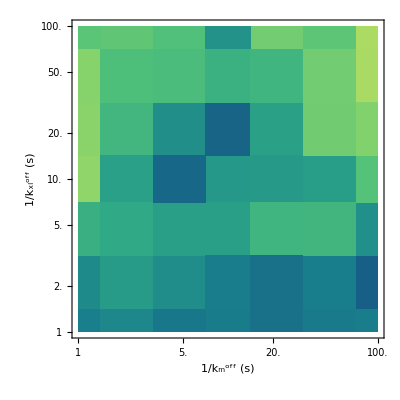

```mathematica
p2
```

```mathematica
Export[figdir<>"/4F.pdf",p2];
Export[figdir<>"/4CFleg.pdf",leg];
```

## Koff / Length (Figs. 4, S3, S4)

### plot setup

```mathematica
grf="/analysis/gr_dr0.05_maxr25t351-400.dat";
grbf="/analysis/gr_barbed_dr0.05_maxr25t351-400.dat";
meshsizef="/analysis/meshsizes_1D_vx0.25_thresh1_t351-400.dat";

(*Plot Options*)
cf=ColorData["BlueGreenYellow"];
cols=Flatten[Table[cf/@ConstantArray[i,3],{i,0,1,0.2}]];
joind=Flatten[ConstantArray[{True,False,False},6]];
pms=Flatten[Table[errbarpms[cf[i],Rectangle[]],{i,0,1,0.2}],1];
fills=Flatten[Table[{i->{i+1}},{i,2,18,3}],1];

lenleg=SwatchLegend[cols[[1;;-1;;3]],lens,LegendLabel->"L (μm)    ",Spacings->0,LegendMarkerSize->15,LegendLayout->"ReversedColumn"];

koffs={0.01,0.02,0.05,0.1,0.2,0.5,1};
lens={1,2,5,8,10,15};
seeds={2,3,4,5};
tixx={Log10[1/#],ToString[1/#]}&/@koffs;
tixxn={Log10[1/#],""}&/@koffs;
ftix={Automatic,{Join[tixx[[1;;-1;;2]],tixxn],tixxn}};

idx[i_]:=Min[Max[4/i,1],350];
idxs[i_]:=With[{start=idx[koffs[[Mod[i-1,10]+1]]]},Range[start,start+50]];

dr=0.05;
maxr=5;
ti=-50;
tf=-1;
```

### 4A

```mathematica
pr={{-0.1,2.1},{0,27}};
```

```mathematica
pkdirs=seedLenXlkoffMkoff5[[{2,3,4,5}]];
```

```mathematica
pkgrs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,pkdirs,{3}];
```

```mathematica
pkgrsmu=Mean[pkgrs];
pkgrserr=StandardDeviation[pkgrs]/Sqrt[Length[pkgrs]];
cs=Table[errcurves[Log10[1/koffs],pkgrsmu[[i]],pkgrserr[[i]]],{i,Length[pkgrsmu]}];
```

```mathematica
p1=ListPlot[Flatten[Map[Reverse,cs,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,FillingStyle->Directive[Opacity[1],Thickness[0.01]],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"1/k_xl^off (s)","⟨g(r)⟩"},PlotLegends->Placed[lenleg,{0.2,0.55}]]
```

```mathematica
Export[figdir<>"/4Aright.svg",p1];
```

```mathematica
mkdirs=seedLenMkoffXlkoff20[[{2,3,4,5}]];
mkgrs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,mkdirs,{3}];
```

```mathematica
mkgrsmu=Mean[mkgrs];
mkgrserr=StandardDeviation[mkgrs]/Sqrt[Length[mkgrs]];
csmk=Table[errcurves[Log10[1/koffs],mkgrsmu[[i]],mkgrserr[[i]]],{i,Length[mkgrsmu]}];
```

```mathematica
p2=ListPlot[Flatten[Map[Reverse,csmk,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"1/k_m^off (s)","⟨g(r)⟩"}]
```

```mathematica
Export[figdir<>"/4Aleft.svg",p2];
```

### S3A

```mathematica
pkc400=cs[[5]];
mkc400=csmk[[5]];
```

```mathematica
pkdirs10=pkdirs[[All,5]];
mkdirs10=mkdirs[[All,5]];
```

```mathematica
grf="/analysis/gr_dr0.05_maxr25t1-400.dat";
```

```mathematica
mkgr=Map[importCheck[#<>grf]&,mkdirs10,{2}];
pkgr=Map[importCheck[#<>grf]&,pkdirs10,{2}];
```

```mathematica
mks400=intmeangr[#,351,400,100,grf]&/@mkdirs10[[All,1]];
```

```mathematica
mkgrstfk=Table[intv[Mean[mkgr[[s,i,idxs[i],1,1;;Round[maxr/dr]]]]],{s,Length[mkgr]},{i,Length[mkgr[[s]]]}];
mkgrtfkmu=Mean[mkgrstfk/maxr];
mkgrtfkerr=StandardDeviation[mkgrstfk/maxr]/Sqrt[Length[mkgrstfk]];
mkctfk=errcurves[Log10[1/koffs],mkgrtfkmu,mkgrtfkerr];
```

```mathematica
pkgrstfk=Table[intv[Mean[pkgr[[s,i,idxs[i],1,1;;Round[maxr/dr]]]]],{s,Length[pkgr]},{i,Length[pkgr[[s]]]}];
pkgrtfkmu=Mean[pkgrstfk/maxr];
pkgrtfkerr=StandardDeviation[pkgrstfk/maxr]/Sqrt[Length[pkgrstfk]];
pkctfk=errcurves[Log10[1/koffs],pkgrtfkmu,pkgrtfkerr];
```

```mathematica
pms2=Join[errbarpms[Red,Disk[],0.05],errbarpms[Red,Rectangle[],0.05]];
pleg=PointLegend[{Black,Black},{"t_f=400 s","t_f=4/k_m^off"},LegendMarkerSize->15,LegendMarkers->{Graphics[Disk[]],Graphics[Rectangle[]]},LabelStyle->FontSize->22,Spacings->0];
```

```mathematica
p1=ListPlot[Reverse/@Join[mkc400,mkctfk],PlotStyle->{Red,Red},Joined->joind,PlotMarkers->pms2,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->Full,FrameTicks->ftix,FrameLabel->{"1/k_m^off (s)","⟨g(r)⟩"},
PlotLegends->Placed[pleg,{0.5,0.4}]]
```

```mathematica
Export[figdir<>"/S3Aleft.svg",p1];
```

```mathematica
p2=ListPlot[Reverse/@Join[pkc400,pkctfk],PlotStyle->{Red,Red},Joined->joind,PlotMarkers->pms2,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->Full,FrameTicks->ftix,FrameLabel->{"1/k_xl^off (s)","⟨g(r)⟩"}]
```

```mathematica
Export[figdir<>"/S3Aright.svg",p2];
```

### S4 A

```mathematica
dirs=seedLenMkoff[[{2,3,4,5}]];
pr={{-0.1,2},{0,16}};
```

```mathematica
mkgrbs=Map[intmeangrb[#,ti,tf,Round[maxr/dr]]/maxr&,dirs,{3}];
```

```mathematica
mkgrbsmu=Mean[mkgrbs];
mkgrbserr=StandardDeviation[mkgrbs]/Sqrt[Length[mkgrbs]];
cs=Table[errcurves[Log10[1/koffs],mkgrbsmu[[i]],mkgrbserr[[i]]],{i,Length[mkgrbsmu]}];
```

```mathematica
p1=ListPlot[Flatten[cs,1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->pr,FrameTicks->ftix,FrameLabel->{"1/k_m^off (s)","⟨g(r_barb)/g(r)⟩"},PlotLegends->Placed[lenleg,{0.2,0.55}]]
```

```mathematica
Export[figdir<>"/S4A.svg",p1];
```

### 4 B

```mathematica
mkgrbbs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grbf]/maxr&,dirs,{3}];
```

```mathematica
mkgrbsmu=Mean[mkgrbbs];
mkgrbserr=StandardDeviation[mkgrbbs]/Sqrt[Length[mkgrbbs]];
cs=Table[errcurves[Log10[1/koffs],mkgrbsmu[[i]],mkgrbserr[[i]]],{i,Length[mkgrbsmu]}];
```

```mathematica
p1=ListLogPlot[Flatten[cs,1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->{{-0.1,2.1},{0.9,170}},FrameTicks->ftix,FrameLabel->{"1/k_m^off (s)","⟨g(r_barb)⟩"}]
```

```mathematica
Export[figdir<>"/4B.svg",p1];
```

### S3B

```mathematica
c1=cs[[5]];
dirs10=dirs[[All,5]];
grbf="/analysis/gr_barbed_dr0.05_maxr25t1-400.dat";
```

```mathematica
grbs=Map[importCheck[#<>grbf]&,dirs10,{2}];
```

```mathematica
grbstfk=Table[intv[Mean[grbs[[s,i,idxs[i],1,1;;maxr/dr]]]]/maxr,{s,Length[grbs]},{i,Length[grbs[[s]]]}];
grbstfkmu=Mean[grbstfk];
grbstfkerr=StandardDeviation[grbstfk]/Sqrt[Length[grbstfk]];
c2=errcurves[Log10[1/koffs],grbstfkmu,grbstfkerr];
```

```mathematica
pms2=Join[errbarpms[forestgreen,Disk[],0.05],errbarpms[forestgreen,Rectangle[],0.05]];
```

```mathematica
p1=ListLogPlot[Join[c1,c2],PlotStyle->{forestgreen,forestgreen},Joined->joind,PlotMarkers->pms2,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->Full,FrameTicks->ftix,FrameLabel->{"1/k_m^off (s)","⟨g(r_barb)⟩"}]
```

```mathematica
Export[figdir<>"/S3B.svg",p1];
```

### S4B

```mathematica
dirs=seedLenXlkoff[[{2,3,4,5}]];
```

```mathematica
xlkgrs=Map[intmeangr[#,ti,tf,Round[maxr/dr],grf]/maxr&,dirs,{3}];
```

```mathematica
xlkmesh=Map[meshavg[#,meshsizef]&,dirs,{3}];
```

```mathematica
xlkmgr=xlkmesh/(xlkgrs);
xlkmgrmu=Mean[xlkmgr];
xlkmgrerr=StandardDeviation[xlkmgr]/Sqrt[Length[xlkmgr]];
cs=Table[errcurves[Log10[1/koffs],xlkmgrmu[[i]],xlkmgrerr[[i]]],{i,Length[xlkmgrmu]}];
```

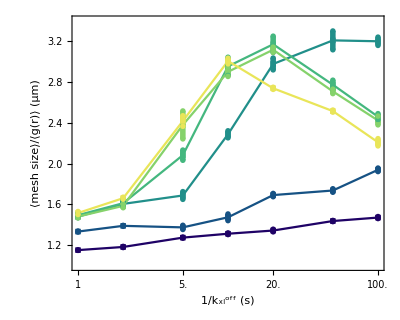

```mathematica
p1=ListPlot[Flatten[Map[Reverse,cs,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,FillingStyle->Directive[Opacity[1],Thickness[0.01]],
Filling->fills,PlotRange->{Full,{1,3.4}},FrameTicks->ftix,FrameLabel->{"1/k_xl^off (s)","⟨mesh size⟩/⟨g(r)⟩ (μm)"}]
```

```mathematica
Export[figdir<>"/S4B.svg",p1];
```

### 4 C

```mathematica
xlkmmu=Mean[xlkmesh];
xlkmerr=StandardDeviation[xlkmesh]/Sqrt[Length[xlkmesh]];
cs=Table[errcurves[Log10[1/koffs],xlkmmu[[i]],xlkmerr[[i]]],{i,Length[xlkmmu]}];
```

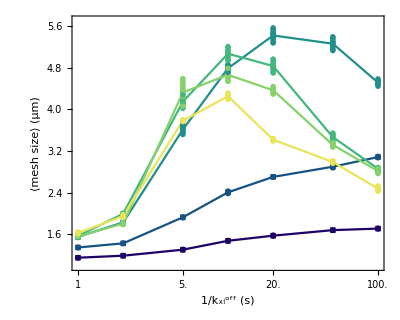

```mathematica
p1=ListPlot[Flatten[Map[Reverse,cs,{2}],1],PlotStyle->cols,Joined->joind,PlotMarkers->pms,PlotRange->{1,5.7},FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->Full,FrameTicks->ftix,FrameLabel->{"1/k_xl^off (s)","⟨mesh size⟩ (μm)"}]
```

```mathematica
Export[figdir<>"/4C.svg",p1];
```

### S3C

```mathematica
dirs10=dirs[[All,5]];
meshcurves400=cs[[5]];
```

```mathematica
meshsizef2="/analysis/meshsizes_1D_vx0.25_thresh1_t1-400.dat";
xlkmeshk=Table[Mean[Flatten[importCheck[dirs10[[s,i]]<>meshsizef2][[idxs[i]]]]],{s,Length[dirs10]},{i,Length[dirs10[[s]]]}];
```

```mathematica
xlkmeshkmu=Mean[xlkmeshk];
xlkmeshkerr=StandardDeviation[xlkmeshk]/Sqrt[Length[xlkmeshk]];
meshcurvesk=errcurves[Log10[1/koffs],xlkmeshkmu,xlkmeshkerr];
```

```mathematica
pms2=Join[errbarpms[Blue,Disk[],0.05],errbarpms[Blue,Rectangle[],0.05]];
p1=ListPlot[Join[Reverse/@meshcurves400,Reverse/@meshcurvesk],PlotStyle->{Blue,Blue},Joined->joind,PlotMarkers->pms2,FillingStyle->Directive[{Opacity[1],Thickness[0.01]}],Filling->fills,PlotRange->{1.3,4.9},FrameTicks->ftix,FrameLabel->{"1/k_xl^off (s)","⟨mesh size⟩ (μm)"}]
```

```mathematica
Export[figdir<>"/S3C.svg",p1];
```